```mathematica
Import["vicon_input.m"]
Import["datasets.m"]
```

```mathematica
annotations = LoadAnnotations[];
reaches = ExtractReaches[currentDataset, annotations];
planeData = ComputeTrackPlaneData[reaches[[2]], 1];
reach = reaches[[2,1,2]];
(*MatrixForm[reaches[[2,1,2]]];*)

(*CTPOffsetPts2D = MatrixForm[planeData[[3,2]] ];*)
OffsetPts2D =Transpose[planeData[[5,2]]];
maxOffset = Max[offsetPts2D[[3]]];

outConic = ComputeConic2D[planeData[[5,2]]];
wristConicParametric = ComputeParametricEllipseFromConic2D[outConic[[1,2]]];
wristConicParametric[[4,2]];
wristConicParametric[[5,2]];
```

```mathematica
reachesAndConics = AnnotationReachAndConics[currentDataset, annotations, 1];
firstReach = reachesAndConics[[3]];
firstReachTrackE = firstReach[[1,2,4,2]];
firstReachTrackS= firstReach[[1,2,5,2]];
firstReachTrack = firstReach[[1,2,1,2]];
CartToHom3D[firstReachTrack]
CartToHom3D[firstReachTrackE]
CartToHom3D[firstReachTrackS]
```

{{-134.319,-134.968,-135.783,-136.714,-137.943,-139.301,-141.1,-143.092,-145.453,-148.04,-151.139,-154.614,-158.462,-162.782,-167.365,-172.587,-178.026,-184.448,-190.747,-197.601,-204.527,-211.858,-219.205,-226.828,-234.352,-241.918,-249.813,-257.515,-265.309,-273.164,-281.15,-289.439,-297.885,-306.31,-315.652,-324.468,-333.271,-342.03,-350.654,-358.974,-367.005,-374.731,-382.721,-390.702,-398.474,-406.346,-414.086,-421.791,-429.273,-436.621,-443.701,-450.741,-457.399,-463.527,-469.43,-474.956,-480.219,-484.745,-489.399,-493.284,-497.376,-501.162,-504.204,-507.207,-509.668,-512.109,-514.234,-515.959,-517.449,-518.76,-520.191,-521.416,-522.384,-523.196,-523.843,-525.455,-526.035,-526.74,-527.328,-527.905,-528.439,-528.993,-529.467,-529.779,-530.145},{-283.696,-283.642,-283.5,-283.186,-282.943,-282.544,-282.251,-282.028,-281.85,-281.379,-281.069,-280.743,-280.354,-279.98,-279.652,-279.573,-279.33,-278.832,-278.626,-278.275,-277.873,-277.48,-277.011,-276.533,-275.996,-275.535,-275.156,-275.059,-275.037,-275.156,-275.226,-275.505,-276.278,-276.53,-276.417,-277.423,-278.372,-279.391,-280.417,-281.409,-282.445,-283.729,-284.634,-285.818,-287.246,-288.821,-290.397,-291.986,-293.712,-295.224,-296.983,-298.471,-300.137,-301.544,-302.922,-304.253,-305.506,-306.645,-307.502,-308.264,-308.977,-309.541,-310.471,-311.022,-311.653,-312.226,-312.717,-313.362,-314.018,-314.874,-315.458,-316.152,-317.014,-317.816,-318.773,-319.071,-319.738,-320.467,-320.91,-321.381,-321.734,-322.155,-322.32,-322.545,-322.675},{172.278,172.535,172.816,173.232,173.703,174.261,174.927,175.587,176.142,176.765,177.385,177.879,178.366,178.823,179.023,179.242,179.297,179.673,179.606,179.603,179.646,179.807,180.031,180.256,180.577,181.036,181.669,181.88,181.94,181.949,181.818,181.693,181.64,181.098,180.689,179.867,178.971,177.996,177.169,176.547,175.806,175.073,174.361,173.655,172.583,171.246,169.904,168.216,166.452,164.645,162.625,160.645,158.654,156.71,154.742,152.878,150.776,148.907,147.01,145.299,143.57,141.882,140.601,139.44,138.328,137.444,136.386,135.48,134.568,133.7,132.977,132.249,131.574,130.878,130.251,129.234,128.646,127.848,127.052,126.297,125.641,124.996,124.427,123.664,123.271},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

{{-202.117,-202.35,-202.685,-203.022,-203.417,-203.873,-204.377,-204.959,-205.546,-206.243,-207.019,-207.868,-208.718,-209.646,-210.563,-211.545,-212.566,-213.755,-215.006,-217.106,-218.496,-220.025,-221.136,-222.822,-224.508,-225.961,-227.86,-229.863,-231.417,-233.964,-236.056,-238.349,-241.191,-243.531,-246.199,-249.488,-251.82,-254.874,-258.121,-261.759,-265.282,-268.192,-271.618,-274.861,-278.025,-282.035,-285.294,-288.436,-292.064,-295.943,-299.152,-302.401,-305.573,-308.743,-311.516,-314.032,-316.974,-319.087,-321.444,-323.617,-325.638,-327.497,-329.236,-330.804,-332.462,-333.665,-334.915,-336.346,-337.508,-338.598,-339.311,-340.19,-341.,-341.738,-342.691,-343.347,-343.936,-344.513,-344.779,-345.491,-345.908,-346.283,-346.679,-346.784,-347.126},{-146.783,-146.459,-146.016,-145.521,-144.968,-144.309,-143.47,-142.563,-141.51,-140.271,-138.892,-137.368,-135.762,-133.942,-132.024,-130.004,-128.013,-125.919,-123.826,-120.449,-118.873,-116.885,-115.553,-113.976,-112.6,-111.536,-110.899,-110.189,-109.884,-109.56,-110.166,-110.58,-111.147,-112.182,-112.716,-113.852,-115.539,-116.942,-118.492,-119.884,-122.03,-124.322,-126.223,-128.569,-130.877,-132.729,-134.865,-137.612,-140.001,-142.44,-144.827,-147.662,-150.89,-153.66,-156.401,-159.453,-162.066,-165.256,-168.053,-170.845,-173.626,-176.386,-179.002,-181.333,-183.235,-185.151,-186.692,-187.754,-188.918,-190.008,-191.414,-192.557,-193.707,-194.876,-195.759,-196.938,-198.055,-199.084,-200.309,-200.938,-201.717,-202.278,-202.749,-203.291,-203.549},{72.8386,73.0528,73.3079,73.6055,73.9413,74.3245,74.7532,75.193,75.6756,76.1733,76.7044,77.2377,77.7353,78.2674,78.8008,79.3422,79.8748,80.4907,81.1727,82.4194,83.1311,84.4121,84.9886,86.0359,87.2341,88.6975,89.8103,91.3329,93.1902,94.7653,96.0276,97.8027,99.3813,101.05,103.341,104.785,106.635,108.66,110.699,112.877,114.446,116.377,118.511,120.364,122.44,124.624,127.144,129.142,131.436,133.677,136.616,139.155,141.4,144.216,147.27,149.938,152.524,154.89,157.375,159.767,162.021,164.081,165.831,167.281,168.662,169.424,170.099,170.812,171.254,171.593,171.664,171.9,172.107,172.237,172.564,172.638,172.723,172.766,172.669,172.845,172.806,172.743,172.61,172.309,172.161},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

{{-44.8953,-45.179,-45.4355,-45.6972,-46.0367,-46.2708,-46.5301,-47.0171,-47.4064,-47.6238,-47.8591,-48.1725,-48.5139,-48.7383,-48.8538,-49.0693,-49.2415,-49.3899,-49.5061,-49.712,-49.8246,-49.9101,-49.9891,-50.0267,-50.1098,-50.1179,-50.1341,-50.2527,-50.2364,-50.5114,-50.7905,-51.2609,-51.6468,-52.4335,-53.0718,-53.7499,-54.4759,-55.2821,-56.1441,-57.2866,-58.4432,-59.8978,-61.2949,-62.6862,-64.0349,-65.4385,-66.9864,-68.3647,-69.7596,-71.166,-72.5635,-74.0115,-75.4753,-77.0083,-78.554,-80.0145,-81.4936,-82.9083,-84.2501,-85.5824,-86.8989,-88.1656,-89.4366,-90.6699,-91.9583,-93.0961,-94.1734,-95.4038,-96.6275,-97.7569,-98.8371,-99.7155,-100.69,-101.549,-102.281,-103.167,-103.879,-104.617,-105.143,-105.741,-106.131,-106.644,-107.019,-107.383,-107.828},{-95.8303,-95.8338,-95.8885,-95.9702,-95.9657,-96.0793,-96.2498,-96.381,-96.4955,-96.6727,-96.7868,-96.8161,-96.8225,-96.7297,-96.6672,-96.5881,-96.5474,-96.4307,-96.3154,-96.2539,-96.1731,-96.1424,-96.0831,-95.9798,-95.873,-95.8061,-95.8232,-95.8556,-95.9801,-96.1303,-96.3475,-96.6469,-96.9576,-97.2154,-97.6724,-98.1385,-98.572,-99.1252,-99.6619,-100.172,-100.753,-101.324,-102.003,-102.703,-103.398,-104.122,-104.819,-105.613,-106.531,-107.481,-108.428,-109.541,-110.551,-111.651,-112.803,-114.026,-115.318,-116.614,-117.888,-119.088,-120.33,-121.527,-122.686,-123.923,-124.868,-125.868,-126.936,-127.838,-128.727,-129.574,-130.275,-131.023,-131.765,-132.466,-133.104,-133.833,-134.406,-134.939,-135.514,-135.963,-136.395,-136.806,-137.17,-137.468,-137.822},{266.35,266.34,266.236,266.262,266.336,266.336,266.329,266.485,266.613,266.605,266.723,266.871,267.1,267.187,267.244,267.44,267.575,267.621,267.679,267.87,267.987,268.142,268.337,268.524,268.839,269.121,269.381,269.801,270.044,270.497,270.794,271.054,271.189,271.758,272.057,272.426,272.703,272.882,272.998,273.035,272.958,273.07,273.102,272.969,272.722,272.663,272.581,272.519,272.41,272.428,272.537,272.793,272.912,273.165,273.502,273.97,274.39,274.867,275.43,275.85,276.493,277.085,277.489,278.018,278.357,278.683,278.799,279.103,279.319,279.479,279.606,279.69,279.774,279.89,279.967,279.985,280.046,280.117,280.199,280.328,280.376,280.472,280.527,280.594,280.667},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

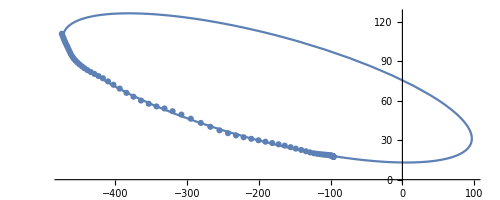

```mathematica
Show[{
ParametricPlot[HomToCart2D[
RigidTrans2D[-1.70815,-187.874, 69.7672].
CartToHom2D[Transpose[{{41.2608 * Cos[ppTheta], 287.188 * Sin[ppTheta]}}]]
], {ppTheta, -Pi, Pi}],
ListPlot[OffsetPts2D](*,
ListPlot[{wristConicParametric[[1,2]]}],
Graphics[
Line[{wristConicParametric[[1,2]] - wristConicParametric[[3,2,1]] * wristConicParametric[[2,2,1]], wristConicParametric[[1,2]] + wristConicParametric[[3,2,1]] * wristConicParametric[[2,2,1]]}
]],
Graphics[
Line[
{wristConicParametric[[1,2]] - wristConicParametric[[3,2,2]] * wristConicParametric[[2,2,2]]
, wristConicParametric[[1,2]] + wristConicParametric[[3,2,2]] * wristConicParametric[[2,2,2]]} 
]]*)
(*,
ListPlot[Transpose[HomToCart2D[RigidTrans2D[,VTSWristCenter[[1]], VTSWristCenter[[2]]].CartToHom2D[{ParametricEllipsePt[WristAxLens[[1]], WristAxLens[[2]], uTheta]}]]]]*)
}]
```

```mathematica
Show[
{
ListPointPlot3D[firstReachTrack
(*, PlotRange->{{-300,300},{-300,300},{-300,300}}*)
, AspectRatio->1]
(*ListPointPlot3D[firstReachTrackE]*)
}]
```

-Graphics3D-

```mathematica
outPts3d={{-134.0870794,-134.7587545,-135.6041169,-136.6004039,-137.8843485,-139.3214272,-141.1879014,-143.2317787,-145.6120317,-148.2496380,-151.3678405,-154.8387525,-158.6794215,-162.9815520,-167.5139121,-172.6680355,-178.0433833,-184.4487177,-190.6892831,-197.5107257,-204.4227094,-211.7553252,-219.1174751,-226.7592982,-234.3052083,-241.8913688,-249.7988420,-257.5002832,-265.2902972,-273.1398291,-281.1168645,-289.3973142,-297.8434733,-306.2624104,-315.5540620,-324.4031791,-333.2400725,-342.0412079,-350.6877530,-358.9952685,-367.0193459,-374.7533622,-382.6743448,-390.5877025,-398.3605787,-406.2687354,-414.0277361,-421.7942820,-429.3642429,-436.7536778,-443.9585820,-451.0326895,-457.7632453,-463.9227795,-469.8448954,-475.3608647,-480.6639091,-485.2197178,-489.7782193,-493.5968038,-497.5284177,-501.1240278,-504.0788068,-506.8270389,-509.1564781,-511.3472819,-513.3330570,-515.0153982,-516.5324027,-517.9626352,-519.3317250,-520.5900828,-521.7081715,-522.7155186,-523.6386544,-525.1015900,-525.8759229,-526.8237418,-527.6140841,-528.3893826,-529.0627625,-529.7622443,-530.3074594,-530.8549450,-531.2561408},{-282.8144369,-282.7377261,-282.6419803,-282.5302814,-282.3881403,-282.2314436,-282.0316722,-281.8177177,-281.5748061,-281.3133894,-281.0147073,-280.6952395,-280.3574222,-279.9982182,-279.6413175,-279.2617569,-278.8951149,-278.4963317,-278.1468281,-277.8079321,-277.5096058,-277.2418028,-277.0224963,-276.8466069,-276.7239749,-276.6512615,-276.6289625,-276.6593779,-276.7422379,-276.8785989,-277.0715337,-277.3298933,-277.6546640,-278.0403847,-278.5386904,-279.0850450,-279.7017124,-280.3878737,-281.1335527,-281.9185396,-282.7423305,-283.5992046,-284.5428933,-285.5549246,-286.6191109,-287.7763190,-288.9882867,-290.2814561,-291.6233853,-293.0157287,-294.4569027,-295.9579273,-297.4711328,-298.9343384,-300.4174466,-301.8716183,-303.3414240,-304.6650188,-306.0505174,-307.2620503,-308.5620305,-309.8015112,-310.8592440,-311.8772131,-312.7676825,-313.6298556,-314.4333510,-315.1314340,-315.7753295,-316.3955663,-317.0018657,-317.5705104,-318.0853448,-318.5572416,-318.9966657,-319.7073496,-320.0909371,-320.5677878,-320.9718095,-321.3740167,-321.7282431,-322.1011867,-322.3955179,-322.6943812,-322.9155463},{173.0733619,173.1837357,173.3215878,173.4825381,173.6875610,173.9138572,174.2028022,174.5128384,174.8656038,175.2462206,175.6824397,176.1507607,176.6481719,177.1798802,177.7114937,178.2811541,178.8365255,179.4477666,179.9915321,180.5286974,181.0132212,181.4626713,181.8481824,182.1797073,182.4393659,182.6333374,182.7645776,182.8232561,182.8135186,182.7335903,182.5802700,182.3440808,182.0219441,181.6186221,181.0772041,180.4663716,179.7621291,178.9652603,178.0874683,177.1531852,176.1637938,175.1267966,173.9770648,172.7365952,171.4251487,169.9920709,168.4844502,166.8692324,165.1868193,163.4352229,161.6164923,159.7167030,157.7963416,155.9349512,154.0441125,152.1864290,150.3052733,148.6084234,146.8295079,145.2718020,143.5982459,142.0006073,140.6357739,139.3210214,138.1699818,137.0546876,136.0145792,135.1103732,134.2759078,133.4717043,132.6851992,131.9472102,131.2787838,130.6658799,130.0949604,129.1712214,128.6724423,128.0522029,127.5265286,127.0030674,126.5419307,126.0563056,125.6729574,125.2836275,124.9954644},{1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000}};
outPts3dE={{-204.0311953,-204.0787658,-204.1475890,-204.2283607,-204.3248440,-204.4477114,-204.6149643,-204.8147650,-205.0673207,-205.3988418,-205.8164056,-206.3392112,-206.9603605,-207.7580328,-208.7013603,-209.8181504,-211.0475343,-212.5000053,-214.0871745,-216.8481042,-218.4030859,-220.3892159,-221.6543186,-223.4754824,-225.2819762,-226.9690686,-228.7093311,-230.7001929,-232.5162733,-234.8554369,-236.7627531,-239.0670352,-241.6687802,-244.0463011,-246.8716880,-249.7914773,-252.3937730,-255.4748619,-258.6916873,-262.1194833,-265.3933906,-268.4919667,-271.8035643,-275.0102800,-278.2116448,-281.6697384,-284.9114386,-288.0885118,-291.4135552,-294.7881204,-298.0120900,-301.2426281,-304.4556384,-307.6087732,-310.6120627,-313.4873147,-316.2777854,-318.9048596,-321.4585372,-323.8897184,-326.2013488,-328.3782179,-330.3638325,-332.0955131,-333.6524520,-334.9292455,-336.0450786,-337.0240914,-337.9013619,-338.7022754,-339.4627364,-340.1983974,-340.9091106,-341.5892737,-342.2527376,-342.8987600,-343.5039846,-344.0618408,-344.5869493,-345.0483612,-345.4483506,-345.7487097,-346.0043105,-346.1824245,-346.3390904},{-147.1048158,-146.7650685,-146.2925580,-145.7636807,-145.1638684,-144.4436690,-143.5298955,-142.5218561,-141.3535492,-139.9633017,-138.3935205,-136.6474273,-134.8152528,-132.7552615,-130.6411588,-128.4802697,-126.4307570,-124.3545335,-122.4227901,-119.7066182,-118.4634828,-117.1197379,-116.3883460,-115.4850849,-114.7451634,-114.1798281,-113.7118813,-113.3072400,-113.0495429,-112.8609462,-112.8173712,-112.8866574,-113.1135929,-113.4490463,-113.9956577,-114.7182723,-115.4891111,-116.5474127,-117.8118019,-119.3289783,-120.9338719,-122.5871949,-124.4933956,-126.4719765,-128.5739461,-130.9833189,-133.3702730,-135.8282501,-138.5249681,-141.3907262,-144.2493128,-147.2319497,-150.3161157,-153.4576569,-156.5567062,-159.6224941,-162.6917558,-165.6672780,-168.6411632,-171.5486467,-174.3837333,-177.1179704,-179.6678450,-181.9362051,-184.0119697,-185.7404469,-187.2707484,-188.6288314,-189.8582231,-190.9910357,-192.0759737,-193.1343084,-194.1650630,-195.1592611,-196.1364505,-197.0950668,-197.9995968,-198.8389311,-199.6339590,-200.3365671,-200.9487176,-201.4102844,-201.8043577,-202.0796694,-202.3223086},{74.8033462,74.8141783,74.8310638,74.8525189,74.8801861,74.9182040,74.9742059,75.0464387,75.1445021,75.2823751,75.4676018,75.7135108,76.0211457,76.4348979,76.9447546,77.5701905,78.2796945,79.1399782,80.1015516,81.8153493,82.7988701,84.0706680,84.8887113,86.0758640,87.2634141,88.3804935,89.5401312,90.8750985,92.0999777,93.6868044,94.9877106,96.5671537,98.3599797,100.0064701,101.9725620,104.0144126,105.8423280,108.0158540,110.2953115,112.7351047,115.0753103,117.2987645,119.6839621,122.0020903,124.3244359,126.8418796,129.2099835,131.5384464,133.9832867,136.4727644,138.8588494,141.2573413,143.6503324,146.0060592,148.2566519,150.4176057,152.5208316,154.5063903,156.4416764,158.2889961,160.0499800,161.7124155,163.2323587,164.5607663,165.7574428,166.7404701,167.6008299,168.3566792,169.0347723,169.6545102,170.2435424,170.8139256,171.3654963,171.8938523,172.4097085,172.9124578,173.3838690,173.8187423,174.2284040,174.5886296,174.9010985,175.1358578,175.3357162,175.4750315,175.5976013},{1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000}};
outPts3dS={{-46.8879814,-46.8894093,-46.8956343,-46.9036229,-46.9060583,-46.9234508,-46.9589306,-47.0076927,-47.0665997,-47.1507019,-47.2194751,-47.2755467,-47.3297794,-47.3296962,-47.3218738,-47.3179190,-49.2054401,-49.3368209,-49.4360745,-49.6710146,-49.7840221,-49.8955296,-50.0009504,-50.0531117,-50.1745866,-50.2343787,-50.3204450,-50.5319588,-50.6193369,-50.9949141,-51.3553165,-51.8816555,-52.3189375,-53.1240304,-53.8314407,-54.5817180,-55.3320487,-56.1676877,-57.0222641,-58.0445739,-59.0830972,-60.3451168,-61.5948519,-62.8198416,-63.9933845,-65.2391313,-66.5592755,-67.8101873,-69.1195791,-70.4645043,-71.8103301,-73.2800390,-74.6909787,-76.1997861,-77.7466061,-79.2847317,-80.8576040,-82.3954222,-83.8844041,-85.3136754,-86.7742091,-88.1748644,-89.5369110,-90.9243674,-92.1830900,-93.3747101,-94.5399389,-95.7335939,-96.9061022,-97.9953386,-98.9804302,-99.8646575,-100.8012031,-101.6524049,-102.3947405,-103.2662145,-103.9611789,-104.6573638,-105.2439719,-105.8190313,-106.2582198,-106.7619108,-107.1597579,-107.5197268,-107.9540461},{-95.9876552,-96.0024264,-96.0572342,-96.1145573,-96.1302434,-96.2278047,-96.3854078,-96.5609564,-96.7418400,-96.9678742,-97.1352650,-97.2636745,-97.3825047,-97.3823259,-97.3654714,-97.3569154,-95.1250116,-95.1631947,-95.1934010,-95.2691668,-95.3075791,-95.3466385,-95.3845666,-95.4036777,-95.4490311,-95.4717750,-95.5049813,-95.5888193,-95.6243319,-95.7823366,-95.9413654,-96.1849441,-96.3962578,-96.8034267,-97.1777623,-97.5891698,-98.0134693,-98.4992482,-99.0087512,-99.6331375,-100.2821020,-101.0882747,-101.9034048,-102.7168559,-103.5082701,-104.3602121,-105.2752285,-106.1529327,-107.0819815,-108.0464769,-109.0213325,-110.0963390,-111.1379973,-112.2617755,-113.4239024,-114.5890774,-115.7900005,-116.9729877,-118.1264075,-119.2407267,-120.3864365,-121.4916551,-122.5723428,-123.6790742,-124.6881551,-125.6477821,-126.5901791,-127.5596382,-128.5158886,-129.4077129,-130.2171358,-130.9459860,-131.7203258,-132.4262039,-133.0434295,-133.7699578,-134.3508239,-134.9340330,-135.4264744,-135.9101318,-136.2801215,-136.7050979,-137.0412603,-137.3457895,-137.7136887},{267.4545241,267.4499551,267.4334230,267.4168033,267.4123687,267.3858066,267.3462504,267.3063870,267.2692460,267.2275983,267.1997034,267.1798094,267.1624640,267.1624893,267.1648904,267.1661166,268.8115775,268.8577506,268.8921523,268.9720768,269.0098256,269.0466648,269.0811395,269.0980756,269.1372178,269.1563358,269.1836896,269.2501250,269.2772598,269.3919995,269.4994867,269.6524614,269.7763917,269.9981659,270.1871797,270.3825650,270.5734210,270.7812999,270.9893987,271.2330866,271.4754558,271.7637862,272.0433744,272.3123187,272.5656849,272.8304595,273.1067392,273.3647597,273.6312002,273.9012562,274.1680619,274.4557480,274.7285261,275.0167399,275.3086700,275.5955753,275.8856323,276.1661065,276.4348478,276.6902855,276.9488317,277.1944894,277.4312794,277.6704091,277.8855724,278.0877323,278.2839938,278.4836049,278.6782788,278.8578953,279.0193250,279.1634117,279.3151885,279.4523925,279.5714737,279.7105892,279.8210019,279.9311412,280.0235823,280.1138816,280.1826312,280.2612492,280.3231739,280.3790715,280.4463484},{1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000}};

ShowArmPose[inPos_, inMinPlot_, inMaxPlot_]:=
Show[{ListPointPlot3D[{firstReachTrack[[inPos]],firstReachTrackE[[inPos]],firstReachTrackS[[inPos]]}, AspectRatio->1, PlotRange->{{inMinPlot, inMaxPlot},{inMinPlot, inMaxPlot},{inMinPlot, inMaxPlot}}],
Graphics3D[Line[{firstReachTrack[[inPos]],firstReachTrackE[[inPos]],firstReachTrackS[[inPos]]}]]}]

Manipulate[
Show[
{
ShowWAMPose[curPos, -1, 1],
ListPointPlot3D[firstReachTrack],
ListPointPlot3D[Transpose[HomToCart3D[outPts3d]], PlotStyle->Red],
ListPointPlot3D[firstReachTrackE],
ListPointPlot3D[Transpose[HomToCart3D[outPts3dE]], PlotStyle->Red],
ListPointPlot3D[firstReachTrackS],
ListPointPlot3D[Transpose[HomToCart3D[outPts3dS]], PlotStyle->Red]
}], {curPos,1,100, 1}]
```

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
Show[{ListPointPlot3D[firstReachTrack], ListPointPlot3D[Transpose[HomToCart3D[outPts3d]], PlotStyle->Red], ListPointPlot3D[Transpose[HomToCart3D[outPts3dE]], PlotStyle->Orange], ListPointPlot3D[Transpose[HomToCart3D[outPts3dS]], PlotStyle->Green]}]
```

-Graphics3D-

```mathematica
normalToPlane = planeData[[1,2,2,2]];
zAxis = {0,0,1};
Cross[normalToPlane,zAxis]

CrossProductMatrix[inVect_]:= {{0, -inVect[[3]], inVect[[2]]},{inVect[[3]],0,-inVect[[1]]},{-inVect[[2]], inVect[[1]],0}}

RotMatBetweenTwoVecs[inVectA_, inVectB_]:= (
vectV = Cross[inVectA, inVectB];
vectV = vectV / Norm[vectV];
crossProductMatrix = CrossProductMatrix[vectV];
IdentityMatrix[3] +
  crossProductMatrix+
((crossProductMatrix * Transpose[crossProductMatrix])*
(1 / (1+inVectA.inVectB)))
)

rotMat = RotMatBetweenTwoVecs[normalToPlane, zAxis]
rotMat.normalToPlane
```

{0.866563,-0.162579,0.}

{{1.,0.,-0.248775},{0.,1.,-2.81185},{0.120018,-0.846148,1.}}

{0.279962,2.19332,-1.18557}

```mathematica
rotMat.Transpose[rotMat]
```

{{1.06189,0.699519,-0.128757},{0.699519,8.90651,-3.658},{-0.128757,-3.658,1.73037}}

```mathematica
{{cos[alpha], -sin[alpha], cX},{sin[alpha], cos[alpha], cY},{0,0,1}}.Transpose[{{a * cos[theta], b * sin[theta], 1}}]
```

{{cX+a cos[alpha] cos[theta]-b sin[alpha] sin[theta]},{cY+a cos[theta] sin[alpha]+b cos[alpha] sin[theta]},{1}}

```mathematica
{{1,0,0},{0,1,0},{0,0,1}}.{a,b,c}
```

{a,b,c}

```mathematica
inPts={{-95.9082688,-95.8747104,-95.9452371,-95.9559921,-96.0233019,-96.0324123,-96.1926715,-96.2925041,-96.4344944,-96.6099703,-96.9567198,-97.2815471,-97.6671550,-98.3693204,-99.2922465,-100.4613193,-102.0218529,-103.9597881,-106.1471417,-108.7372741,-111.6624229,-115.0365681,-118.9767426,-123.4575903,-128.6265266,-134.4033988,-140.9027600,-148.5295703,-155.7540445,-163.8252600,-172.4327856,-181.2996149,-190.6963846,-200.3685783,-210.4464470,-221.1485244,-231.7740968,-242.8833941,-254.7383374,-267.4633663,-280.7810845,-294.7076345,-307.7970227,-320.0598394,-331.3162451,-342.4659543,-353.2502866,-364.0054433,-374.4715024,-384.2640579,-393.7259316,-402.4664971,-409.9437979,-417.1151508,-423.1971415,-428.8169547,-433.9433737,-438.4105196,-442.5564784,-446.1313366,-449.5748825,-452.6009544,-455.3093479,-457.6217950,-459.6557671,-461.6443082,-463.1987135,-464.7572887,-466.2758762,-467.7248434,-469.1931821,-470.5165761,-471.8218475,-473.1332608,-474.2850726},{17.3009342,17.3263571,17.3713359,17.4723311,17.5604366,17.7757417,17.6852915,17.7009312,17.7517015,17.7729024,17.9704611,18.0188090,18.1365785,18.2569592,18.3923821,18.4606736,18.6318292,18.7514949,18.9432898,19.0414188,19.2013731,19.4171234,19.7040376,20.0947227,20.7430425,21.6250055,22.5993136,23.6041011,24.6970296,25.8965897,26.8984767,27.8575022,28.8612817,29.9428020,31.0884327,32.2672130,33.6925397,35.3412268,37.5194802,40.2162880,43.1484805,46.3423838,49.4897812,52.0449228,54.1559148,55.7069873,57.7182546,60.1711278,63.0808330,66.0037759,69.2237607,72.1876900,74.7497193,77.1218977,78.7799574,80.3798764,81.8538673,83.2368772,84.6747294,86.1333020,87.6121321,89.0803824,90.5537918,92.0071204,93.5913884,95.2991678,97.1426719,98.8888522,100.7827246,102.3840192,104.0716252,105.6870811,107.4920651,109.2917872,110.9835210},{-348.3138219,-348.0499346,-347.7670250,-347.5630806,-347.2651128,-347.1169584,-346.8087301,-346.6610586,-346.5231124,-346.4040968,-346.3973634,-346.2407149,-346.1439943,-346.2969264,-346.3039290,-346.5266980,-346.7229643,-347.1481692,-347.4800261,-347.7956682,-348.2789695,-348.5998298,-349.0025892,-349.3481728,-349.9128712,-350.3432642,-350.9337979,-351.4249613,-351.6189735,-352.0540415,-352.3799866,-352.6819840,-352.8772192,-353.0270774,-353.1125106,-353.4697352,-353.6787878,-353.8749388,-354.0428520,-354.2423485,-354.1231311,-353.4800233,-352.7241763,-351.9940925,-351.0642340,-350.3232963,-349.6336266,-348.8388854,-347.8828090,-346.9160699,-345.8564344,-345.0582867,-344.4892585,-343.9588513,-343.7257426,-343.6129234,-343.6126222,-343.7571637,-344.0092467,-344.3350921,-344.7306706,-345.2209933,-345.8429667,-346.6217110,-347.5948869,-348.5816618,-349.8464851,-350.7976132,-351.9553472,-352.7205393,-353.4277566,-353.9316063,-354.3595506,-354.4896030,-354.4869192}};
outPts={{-95.8563208,-95.8251697,-95.8984218,-95.9185536,-95.9927797,-96.0199485,-96.1714009,-96.2716935,-96.4169194,-96.5929032,-96.9539578,-97.2805433,-97.6732998,-98.3807659,-99.3083485,-100.4748248,-102.0382041,-103.9715540,-106.1585054,-108.7358669,-111.6502754,-115.0140426,-118.9438006,-123.4181311,-128.5980134,-134.4030151,-140.9313315,-148.5757946,-155.8305981,-163.9321613,-172.5335519,-181.3794803,-190.7443673,-200.3806461,-210.4146753,-221.0528548,-231.6398012,-242.7223588,-254.6029521,-267.4051726,-280.8120170,-294.8425589,-308.0423190,-320.3167469,-331.5148195,-342.4641130,-353.1278509,-363.8350501,-374.3497586,-384.2121001,-393.8195194,-402.6697153,-410.2231298,-417.4179695,-423.3785382,-428.8694371,-433.8424457,-438.1699089,-442.2008480,-445.7207397,-449.1029017,-452.1040526,-454.8208569,-457.1904314,-459.3810813,-461.5689157,-463.4972323,-465.3675076,-467.2593914,-468.9016621,-470.4698362,-471.6662726,-472.3551610,-472.3454077,-472.0847813},{17.9084861,17.9058292,17.9120777,17.9137956,17.9201314,17.9224513,17.9353919,17.9439689,17.9563994,17.9714797,18.0024777,18.0305842,18.0644708,18.1257448,18.2065391,18.3088733,18.4473005,18.6204915,18.8190559,19.0566595,19.3299782,19.6515094,20.0352984,20.4828564,21.0149011,21.6286765,22.3407768,23.2036528,24.0511710,25.0302194,26.1070187,27.2543061,28.5128056,29.8548876,31.3032932,32.8960323,34.5401128,36.3252252,38.3132247,40.5440363,42.9824525,45.6517845,48.2792297,50.8304174,53.2552998,55.7233444,58.2272767,60.8507222,63.5454459,66.1929299,68.8991011,71.5197961,73.8689609,76.2190778,78.2631703,80.2376355,82.1148134,83.8294896,85.5072337,87.0478163,88.6077103,90.0707965,91.4734214,92.7712574,94.0476284,95.4151550,96.7202308,98.1065787,99.6822978,101.2723573,103.1480030,105.1531410,107.4195552,109.1715779,110.2267438},{1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000}};
fixedThetas={{3.4907598,0.3492828,0.3490108,0.3489360,0.3486603,0.3485595,0.3479971,0.3476248,0.3470858,0.3464327,0.3450933,0.3438823,0.3424265,0.3398061,0.3363738,0.3320630,0.3262949,0.3191762,0.3111425,0.3016993,0.2910523,0.2788026,0.2645418,0.2483661,0.2297152,0.2089008,0.1855911,0.1584102,0.1327101,0.1040977,0.0737951,0.0426824,0.0097678,-0.0241124,-0.0594454,-0.0970156,-0.1345700,-0.1741202,-0.2168645,-0.2634263,-0.3128759,-0.3655506,-0.4161536,-0.4643024,-0.5093160,-0.5545062,-0.5998264,-0.6468575,-0.6948031,-0.7416617,-0.7894167,-0.8356290,-0.8771065,-0.9187262,-0.9550858,-0.9903976,-1.0241876,-1.0552756,-1.0859353,-1.1143289,-1.1433438,-1.1708298,-1.1974544,-1.2223539,-1.2471128,-1.2739669,-1.2999398,-1.3279360,-1.3603171,-1.3936670,-1.4339917,-1.4784556,-1.5307016,-1.5728069,-1.5990078}};
speed={{-3.1414770,-0.0002721,-0.0000748,-0.0002756,-0.0001009,-0.0005623,-0.0003723,-0.0005390,-0.0006531,-0.0013394,-0.0012110,-0.0014557,-0.0026204,-0.0034323,-0.0043108,-0.0057682,-0.0071187,-0.0080337,-0.0094431,-0.0106471,-0.0122497,-0.0142608,-0.0161756,-0.0186509,-0.0208144,-0.0233097,-0.0271809,-0.0257001,-0.0286123,-0.0303026,-0.0311127,-0.0329146,-0.0338802,-0.0353330,-0.0375701,-0.0375545,-0.0395502,-0.0427442,-0.0465618,-0.0494496,-0.0526747,-0.0506031,-0.0481488,-0.0450135,-0.0451903,-0.0453202,-0.0470310,-0.0479457,-0.0468585,-0.0477550,-0.0462123,-0.0414776,-0.0416197,-0.0363596,-0.0353118,-0.0337899,-0.0310881,-0.0306596,-0.0283936,-0.0290149,-0.0274860,-0.0266247,-0.0248995,-0.0247589,-0.0268540,-0.0259730,-0.0279961,-0.0323811,-0.0333499,-0.0403247,-0.0444638,-0.0522460,-0.0421053,-0.0262008}};
acceleration={{3.1412049,0.0001973,-0.0002009,0.0001748,-0.0004614,0.0001900,-0.0001667,-0.0001140,-0.0006863,0.0001284,-0.0002447,-0.0011647,-0.0008119,-0.0008785,-0.0014574,-0.0013505,-0.0009150,-0.0014094,-0.0012039,-0.0016026,-0.0020111,-0.0019148,-0.0024753,-0.0021635,-0.0024954,-0.0038711,0.0014808,-0.0029122,-0.0016903,-0.0008101,-0.0018018,-0.0009656,-0.0014528,-0.0022371,0.0000157,-0.0019957,-0.0031940,-0.0038176,-0.0028878,-0.0032251,0.0020716,0.0024543,0.0031352,-0.0001767,-0.0001299,-0.0017109,-0.0009146,0.0010872,-0.0008965,0.0015427,0.0047347,-0.0001421,0.0052601,0.0010477,0.0015219,0.0027019,0.0004284,0.0022660,-0.0006213,0.0015290,0.0008613,0.0017252,0.0001405,-0.0020951,0.0008810,-0.0020232,-0.0043850,-0.0009688,-0.0069748,-0.0041391,-0.0077822,0.0101407,0.0159045}};
jerk={{-3.1410076,-0.0003982,0.0003756,-0.0006362,0.0006515,-0.0003567,0.0000527,-0.0005723,0.0008147,-0.0003731,-0.0009200,0.0003528,-0.0000666,-0.0005789,0.0001069,0.0004355,-0.0004944,0.0002055,-0.0003987,-0.0004085,0.0000963,-0.0005605,0.0003118,-0.0003319,-0.0013758,0.0053519,-0.0043930,0.0012219,0.0008801,-0.0009917,0.0008362,-0.0004872,-0.0007843,0.0022528,-0.0020114,-0.0011983,-0.0006235,0.0009297,-0.0003373,0.0052967,0.0003827,0.0006809,-0.0033120,0.0000468,-0.0015810,0.0007962,0.0020018,-0.0019837,0.0024393,0.0031920,-0.0048768,0.0054022,-0.0042124,0.0004742,0.0011800,-0.0022735,0.0018376,-0.0028874,0.0021503,-0.0006677,0.0008639,-0.0015846,-0.0022356,0.0029761,-0.0029042,-0.0023619,0.0034162,-0.0060060,0.0028356,-0.0036431,0.0179229,0.0057638}};
```

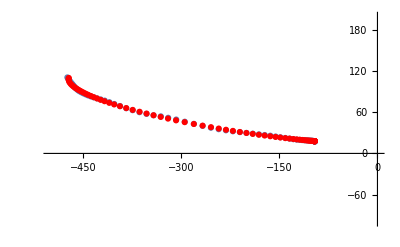

```mathematica
Show[{
ListPlot[Transpose[{inPts[[1]],inPts[[2]]}], PlotRange->{{-500,0}, {-100,200}}],
ListPlot[Transpose[HomToCart2D[outPts]], PlotStyle->Red]
}]
```

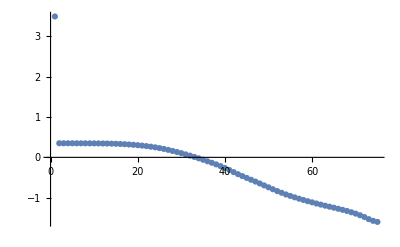

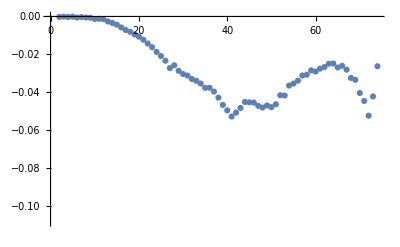

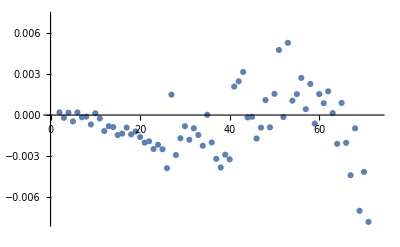

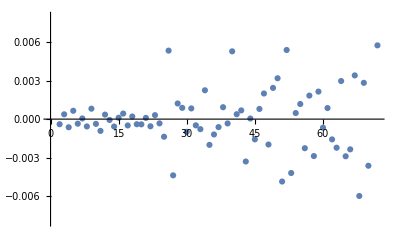

```mathematica
ListPlot[fixedThetas[[1]]]
ListPlot[speed[[1]]]
ListPlot[acceleration[[1]]]
ListPlot[jerk[[1]]]
```

```mathematica
outPts={{11.7664384,11.7909748,11.8143028,11.8363994,11.8572426,11.8768119,11.8950881,11.9120531,11.9276901,11.9419837,11.9549198,11.9664856,11.9766698,11.9854622,11.9928543,11.9988386,12.0034093,12.0065619,12.0082933,12.0086018,12.0074870,12.0049500,12.0009935,11.9956211,11.9888384,11.9806519,11.9710698,11.9601015,11.9477577,11.9340508,11.9189943,11.9026029,11.8848928,11.8658817,11.8455881,11.8240322,11.8012352,11.7772196,11.7520090,11.7256285,11.6981040,11.6694627,11.6397328,11.6089437,11.5771257,11.5443104,11.5105300,11.4758179,11.4402084,11.4037365,11.3664384,11.3283507,11.2895111,11.2499580,11.2097302,11.1688677,11.1274106,11.0853999,11.0428771,10.9998840,10.9564632,10.9126575,10.8685101,10.8240646,10.7793648,10.7344550,10.6893793,10.6441823,10.5989085,10.5536028,10.5083097,10.4630739,10.4179402,10.3729529,10.3281567,10.2835956,10.2393137,10.1953545,10.1517618,10.1085780,10.0658462,10.0236084,9.9819063,9.9407811,9.9002733,9.8604229,9.8212693,9.7828511,9.7452063,9.7083718,9.6723841,9.6372789,9.6030905,9.5698528,9.5375987,9.5063599,9.4761673,9.4470507,9.4190387,9.3921591},{0.4671233,0.4474873,0.4262917,0.4035574,0.3793068,0.3535640,0.3263541,0.2977041,0.2676424,0.2361985,0.2034035,0.1692898,0.1338909,0.0972419,0.0593789,0.0203394,-0.0198382,-0.0611144,-0.1034481,-0.1467978,-0.1911207,-0.2363729,-0.2825099,-0.3294861,-0.3772551,-0.4257699,-0.4749826,-0.5248444,-0.5753063,-0.6263185,-0.6778305,-0.7297917,-0.7821507,-0.8348557,-0.8878549,-0.9410958,-0.9945261,-1.0480929,-1.1017434,-1.1554245,-1.2090834,-1.2626671,-1.3161228,-1.3693976,-1.4224390,-1.4751946,-1.5276124,-1.5796406,-1.6312279,-1.6823235,-1.7328767,-1.7828379,-1.8321576,-1.8807872,-1.9286787,-1.9757849,-2.0220592,-2.0674560,-2.1119304,-2.1554387,-2.1979378,-2.2393859,-2.2797419,-2.3189662,-2.3570199,-2.3938654,-2.4294666,-2.4637882,-2.4967964,-2.5284585,-2.5587433,-2.5876210,-2.6150631,-2.6410424,-2.6655333,-2.6885117,-2.7099548,-2.7298416,-2.7481523,-2.7648690,-2.7799751,-2.7934557,-2.8052975,-2.8154888,-2.8240196,-2.8308815,-2.8360676,-2.8395729,-2.8413938,-2.8415287,-2.8399774,-2.8367413,-2.8318237,-2.8252295,-2.8169651,-2.8070388,-2.7954602,-2.7822409,-2.7673938,-2.7509337},{1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000}};
```

```mathematica
HomToCart2D[outPts][[1]]
```

{11.7664,11.791,11.8143,11.8364,11.8572,11.8768,11.8951,11.9121,11.9277,11.942,11.9549,11.9665,11.9767,11.9855,11.9929,11.9988,12.0034,12.0066,12.0083,12.0086,12.0075,12.005,12.001,11.9956,11.9888,11.9807,11.9711,11.9601,11.9478,11.9341,11.919,11.9026,11.8849,11.8659,11.8456,11.824,11.8012,11.7772,11.752,11.7256,11.6981,11.6695,11.6397,11.6089,11.5771,11.5443,11.5105,11.4758,11.4402,11.4037,11.3664,11.3284,11.2895,11.25,11.2097,11.1689,11.1274,11.0854,11.0429,10.9999,10.9565,10.9127,10.8685,10.8241,10.7794,10.7345,10.6894,10.6442,10.5989,10.5536,10.5083,10.4631,10.4179,10.373,10.3282,10.2836,10.2393,10.1954,10.1518,10.1086,10.0658,10.0236,9.98191,9.94078,9.90027,9.86042,9.82127,9.78285,9.74521,9.70837,9.67238,9.63728,9.60309,9.56985,9.5376,9.50636,9.47617,9.44705,9.41904,9.39216}

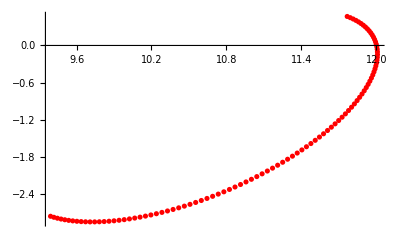

```mathematica
Show[{
ListPlot[Transpose[HomToCart2D[outPts]], PlotStyle->Red]
}]
```

```mathematica
k = {{0, 1, 2, 3, 4, 5}};
```

```mathematica
evidenceMat = 
{{6.53957*Exp[-170],
1.03731*Exp[-159],
2.79047*Exp[-154],
3.34661*Exp[-156],
3.36066*Exp[-156],
5.26404*Exp[-158]}}
likelihoodMat = 
{{1.67505*Exp[-176],
3.47563*Exp[-157],
1.40185*Exp[-151],
1.75257*Exp[-151],
1.85833*Exp[-151],
1.87136*Exp[-151]}};
```

{{9.67135×10^-74,9.18514×10^-70,3.66714×10^-67,5.95204×10^-68,5.97703×10^-68,1.26704×10^-68}}

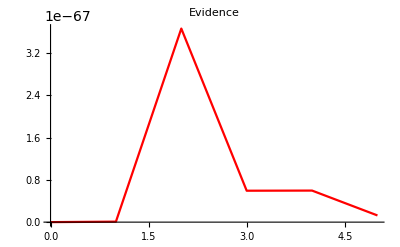

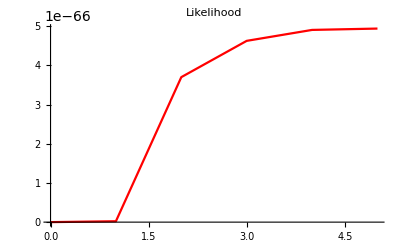

```mathematica
Show[{
ListPlot[Transpose[{k[[1]],evidenceMat[[1]]}], PlotStyle->Red, Joined -> True, PlotRange->All,AxesStyle->Black, 
PlotLabel->HoldForm[Evidence],LabelStyle->{12,GrayLevel[0],Bold}]
}]
Show[{
ListPlot[Transpose[{k[[1]],likelihoodMat[[1]]}], PlotStyle->Red, Joined -> True, PlotRange->All,AxesStyle->Black, 
PlotLabel->HoldForm[Likelihood],LabelStyle->{12,GrayLevel[0],Bold}]
}]
```

```mathematica
outPts2dHat={{-137.1188930,-137.7884363,-138.6312518,-139.6246857,-140.9044883,-142.3370593,-144.1979138,-146.2357612,-148.6092699,-151.2393930,-154.3490510,-157.8105259,-161.6428478,-165.9336314,-170.4557068,-175.5986702,-180.9633540,-187.3567187,-193.5871259,-200.3973420,-207.3001824,-214.6249888,-221.9792924,-229.6135923,-237.1560939,-244.7371348,-252.6421896,-260.3401857,-268.1326647,-275.9847434,-283.9637354,-292.2491475,-300.7014234,-309.1281873,-318.4303744,-327.2913708,-336.1424417,-344.9585384,-353.6218794,-361.9484153,-369.9904940,-377.7450951,-385.6880004,-393.6262484,-401.4247303,-409.3602076,-417.1489698,-424.9465147,-432.5499043,-439.9731366,-447.2130734,-454.3241200,-461.0928244,-467.2880619,-473.2469701,-478.7990734,-484.1387048,-488.7283318,-493.3211434,-497.1699977,-501.1333247,-504.7601843,-507.7404711,-510.5151684,-512.8667717,-515.0799875,-517.0856537,-518.7854609,-520.3200051,-521.7654197,-523.1485825,-524.4217171,-525.5524137,-526.5726476,-527.5062276,-528.9875831,-529.7716660,-530.7310414,-531.5319275,-532.3165634,-532.9996405,-533.7099176,-534.2610944,-534.8158710,-535.2229969},
{31.4991305,31.3257947,31.1088402,30.8548874,30.5305581,30.1712914,29.7105755,29.2137629,28.6452970,28.0281642,27.3158647,26.5450899,25.7189109,24.8277791,23.9273534,22.9516197,21.9886201,20.9140436,19.9433160,18.9685861,18.0726205,17.2231958,16.4752968,15.8101624,15.2643071,14.8271200,14.4902547,14.2789782,14.1824542,14.2046110,14.3499221,14.6318159,15.0569161,15.6190055,16.3998105,17.3000421,18.3516676,19.5505528,20.8758757,22.2871987,23.7782766,25.3351369,27.0510117,28.8884359,30.8128121,32.8923709,35.0525413,37.3332959,39.6710970,42.0619432,44.4969565,46.9878269,49.4501110,51.7818590,54.0950652,56.3124821,58.5015784,60.4274961,62.3957482,64.0767623,65.8378725,67.4762345,68.8416624,70.1284223,71.2306923,72.2779172,73.2351620,74.0525524,74.7952974,75.4990894,76.1763735,76.8030684,77.3622911,77.8690142,78.3344718,79.0765131,79.4710031,79.9553127,80.3609846,80.7596348,81.1076605,81.4705067,81.7527521,82.0374374,82.2467359},{1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000,1.0000000}};
```

```mathematica
Show[{
ListPointPlot3D[firstReachTrack], ListPointPlot3D[Transpose[HomToCart3D[outPts3d]], PlotStyle->Red],
ListPlot[Transpose[HomToCart2D[outPts2dHat]], PlotStyle->Red]
}]
```